# MolecularComplexity

Compute the molecular complexity (C_m) of a given molecule

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
MolecularComplexity[mol_]:=Module[{molec=Molecule[mol],aInds,aSyms,indTsym,symAtoms,symAtomsNoH,indTval,indTcon,bondPairs,bondIndPairs,bondIndsNoH,bondIndPairsNoH,ind,jnd,atomI,vi,bi,di,dj,bondedAs,ei,eAs,si,vj,bj,sj,ej,out,terms,atomII,atomIIpos,jnds,nonEqTerms,eqTerms,allTerms},
aInds=MoleculeValue[molec,"AtomIndex"];(*  atom indices *)
aSyms=MoleculeValue[molec,"AtomicSymbol"];
indTsym=AssociationThread[aInds,aSyms];(* atom indicex -> atomic symbol *)
symAtoms=MoleculeValue[molec,"SymmetryEquivalentAtoms"];
symAtomsNoH=Select[Thread[{TakeList[aSyms,Length[#]&/@symAtoms],symAtoms}],Not@MemberQ[#[[1]],"H"]&][[All,2]];(* lists of symmetrically equivalent atoms *)
indTval=AssociationThread[MoleculeValue[molec,"AtomIndex"],MoleculeValue[molec,"OuterShellElectronCount"]];(* atom index -> valence *)
bondPairs=Lookup[indTsym,#]&/@MoleculeValue[molec,"BondedAtomIndices"];(* list of lists of bonded atom indices *)
bondIndPairs=Thread[{bondPairs,MoleculeValue[molec,"BondedAtomIndices"]}];(* list of pairs of {bonded atom symbols, bonded atom indices} *)
bondIndsNoH=Select[bondIndPairs,Not@MemberQ[#[[1]],"H"]&][[All,2]]; (* list of lists of bonded indices with H removed *)
bondIndPairsNoH=Select[bondIndPairs,Not@MemberQ[#[[1]],"H"]&]; 


terms=Table[
atomI=symAtomsNoH[[i]];
If[Length[atomI]==1,(* if there are no equivalent atoms *)

vi=indTval[First[atomI]];
bi=Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}];
di=(
bondedAs=Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&];
Length@DeleteDuplicates@Table[Select[symAtomsNoH,MemberQ[#,bondedAs[[m]]]&],{m,1,Length@bondedAs}]
);
ei=(
eAs=Prepend[Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&],First[atomI]];
Length@DeleteDuplicates@Lookup[indTsym,eAs]
);
si=(
MoleculeValue[molec,{"AtomChirality",First[atomI]}]/.{"R"->2,"S"->2,"Unspecified"->2,None->1}
);

{di,ei,si,vi,bi}
,(* if there is more than 1 equivalent atom *)
vi=indTval[First[atomI]];
bi=Total[MoleculeValue[molec,{"BondType",#}]&/@Select[bondIndPairsNoH,MemberQ[#[[2]],First[atomI]]&][[All,2]]/.{"Single"->1,"Double"->2,"Triple"->3,"Aromatic"->2}];
di=(
bondedAs=Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&];
Length@DeleteDuplicates@Table[Select[symAtomsNoH,MemberQ[#,bondedAs[[m]]]&],{m,1,Length@bondedAs}]
);
ei=(
eAs=Prepend[Select[Flatten[Select[bondIndsNoH,MemberQ[#,First[atomI]]&]],#≠First[atomI]&],First[atomI]];
Length@DeleteDuplicates@Lookup[indTsym,eAs]
);
si=(
MoleculeValue[molec,{"AtomChirality",First[atomI]}]/.{"R"->2,"S"->2,"Unspecified"->2,None->1}
);

Table[{di,ei,si,vi,bi},Length@atomI]
],{i,1,Length@symAtomsNoH}];

nonEqTerms=Select[terms,Not[MatrixQ[#]]&];
eqTerms=Flatten[Select[terms,MatrixQ[#]&],1];
allTerms=Join[nonEqTerms,eqTerms];

If[Length[eqTerms]>0,
N[Sum[(
allTerms[[All,1]][[s1]]*allTerms[[All,2]][[s1]]*allTerms[[All,3]][[s1]]*Log2[(allTerms[[All,4]][[s1]]*allTerms[[All,5]][[s1]])])
,{s1,1,Length@allTerms}]+Sum[(-0.5*eqTerms[[All,1]][[j1]]*eqTerms[[All,2]][[j1]]*eqTerms[[All,3]][[j1]]*Log2[(eqTerms[[All,4]][[j1]]*eqTerms[[All,5]][[j1]])]),{j1,1,Length@eqTerms}]]
,
N[Sum[
allTerms[[All,1]][[s2]]*allTerms[[All,2]][[s2]]*allTerms[[All,3]][[s2]]*Log2[allTerms[[All,4]][[s2]]*allTerms[[All,5]][[s2]]]
,{s2,1,Length@allTerms}]]
]
]
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

MolecularComplexity[mol]

returns the molecular complexity for Molecule mol.

MolecularComplexity[str]

returns the molecular complexity for the input SMILES or InChI string str.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

Molecular complexity (C_m) can be defined as the sum taking the following form:

C_m = ∑_i  d_i e_i s_i log_2 (V_i b_i) - 1/2 ∑_i d_j e_j s_j log_2 (V_j b_j)
where V_i is the number of valence electrons, b_i is the total number of bonds to any atom with V_i b_i > 1, d_i is the number of chemically nonequivalent bonds to atoms with V_i b_i > 1,  e_i is the number of different atoms in atom i's microenvironment, and s_i is the number of possible isomeric structures at position i.

MolecularComplexity only supports single molecules and will fail if given a list of molecules as input.

MolecularComplexity will return an error and Indeterminate for 0 complexity entities.

MolecularComplexity utilizes MoleculeValue's equivalent atoms, which may differ slightly from true chemical equivalence.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

A single SMILES/InChI string or a Molecule as input. By default, it returns a numerical output corresponding to the C_m of the molecule:

```mathematica
MolecularComplexity["Cn1c(=O)c2c(ncn2C)n(C)c1=O"]
```

280.766

Using a Molecule as input:

```mathematica
m=Molecule["Cn1c(=O)c2c(ncn2C)n(C)c1=O"]
```

Molecule[…]

```mathematica
MolecularComplexity[m]
```

280.766

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Possible Issues

Zero complexity inputs return an error and Indeterminate:

```mathematica
MolecularComplexity["methane"]
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

Indeterminate

```mathematica
MolecularComplexity["[Na+]"]
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

Indeterminate

While providing input in the form of an InChI string works, providing an InChI key string will cause an error:

```mathematica
MolecularComplexity[Molecule["ethanol"]["InChI"]]
```

19.1699

```mathematica
MolecularComplexity[Molecule["ethanol"]["InChIKey"]]
```

Molecule::nintrp: Unable to interpret LFQSCWFLJHTTHZ-UHFFFAOYSA-N as a name or chemical identifier.

MoleculeValue::mol: Argument Molecule[LFQSCWFLJHTTHZ-UHFFFAOYSA-N] is not a valid molecule.

General::stop: Further output of MoleculeValue::mol will be suppressed during this calculation.

TakeList::splist: MoleculeValue[1,0] is not a list of sequence specifications.

First::normal: Nonatomic expression expected at position 1 in First[SymmetryEquivalentAtoms].

General::stop: Further output of First::normal will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 3 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

{{},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}}

### Neat Examples

Show that the trend in molecular complexity of alkanes with increasing (CH_2) groups from 1 to 10 is linear:

```mathematica
complexities=MolecularComplexity[#]&/@{"propane","butane","pentane","hexane","heptane","octane","nonane","decane","undecane","dodecane"};
```

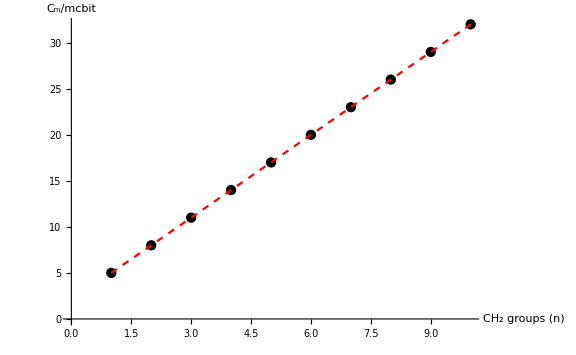

```mathematica
Show[ListPlot[Thread[{Range[1,10],complexities}],AxesLabel->{"CH_2 groups (n)","C_m/mcbit"},PlotStyle->Black],Plot[Evaluate[Fit[Thread[{Range[1,10],complexities}],{1,x},x]],{x,1,10},PlotStyle->{Red,Dashed}],ImageSize->Large]
```

Calculate the change in complexity for a diels-alder reaction:

```mathematica
(* define the reactants and product *)
```

```mathematica
butadiene=Molecule["1,3-butadiene"];
ethene=Molecule["ethene"];
cyclohexene=Molecule["cyclohexene"];
```

```mathematica
(* compute the complexities and find the difference *)
```

```mathematica
cButadiene=MolecularComplexity[butadiene];
cEthene=MolecularComplexity[ethene];
cCyclohexene=MolecularComplexity[cyclohexene];
```

```mathematica
cDiff=cCyclohexene-(cButadiene+cEthene);
```

```mathematica
(* Display the results *)
```

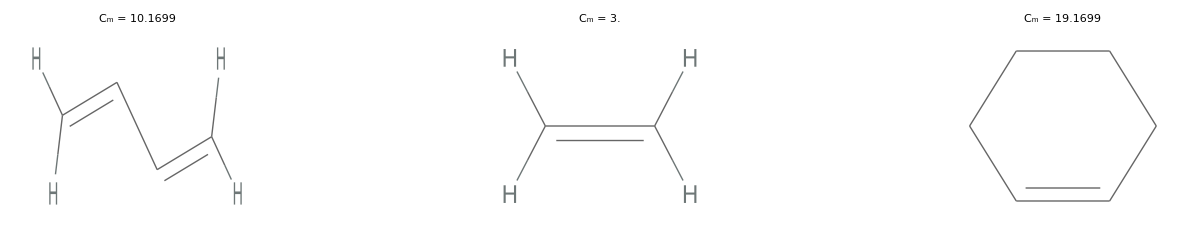

```mathematica
GraphicsRow[{MoleculePlot[butadiene,PlotLabel->"C_m = "<>ToString@MolecularComplexity[butadiene],ImageSize->Small],Graphics[Text@Style["+",40],BaselinePosition->Center,ImageSize->100],MoleculePlot[ethene,PlotLabel->"C_m = "<>ToString@MolecularComplexity[ethene],ImageSize->Small],Graphics[Text@Style["→",40],BaselinePosition->Center,ImageSize->100],MoleculePlot[Molecule@"cyclohexene",PlotLabel->"C_m = "<>ToString@MolecularComplexity[cyclohexene],ImageSize->Small],Graphics[Text@Style["ΔC_m = "<>ToString@cDiff,15],BaselinePosition->Center,ImageSize->100]}]
```

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

William Borrelli <wborrelli@fordham.edu>

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Chemistry

Cheminformatics

Computational Chemistry

Graph Theory

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

Molecule

MoleculeValue

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

Resource Name (resources from any Wolfram repository)

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

[1] Böttcher, T. An Additive Definition of Molecular Complexity. J. Chem. Inf. Model. 2016, 56 (3), 462–470. https://doi.org/10.1021/acs.jcim.5b00723.

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

https://doi.org/10.1021/acs.jcim.5b00723

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.